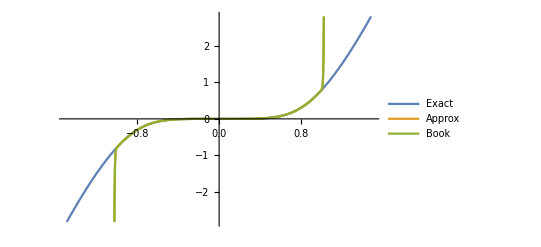

```mathematica
Plot[
{(x^2)ArcTan[x^3],
∑_(n=0)^40 (3(-1)^n)/(6n+3)x^(6n+5),
∑_(n=0)^40 (-1)^n/(2n+1)x^(6n+5)},
{x, -1.5, 1.5},
PlotLegends->{"Exact", "Approx", "Book"}]
```

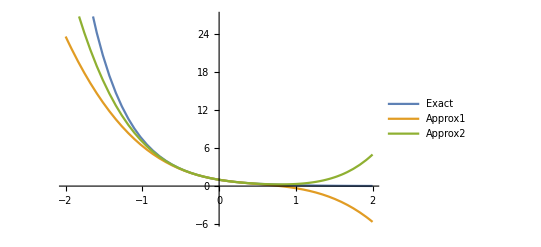

```mathematica
Plot[
{
Exp[-2x],
1 - 2x + 2x^2 - (4/3)x^3,
∑_(n=0)^4 (((-1)^n)2^n)/(n!)x^n,
},
{x, -2, 2},
PlotLegends->{"Exact", "Approx1", "Approx2"}]
```

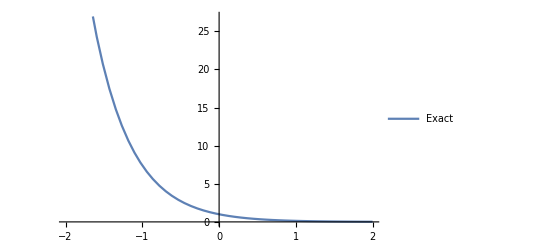

```mathematica
Plot[
{
Exp[-2x],
},
{x, -2, 2},
PlotLegends->{"Exact"}]
```

```mathematica
Manipulate[
Plot[function[frequency * x + shift], {x, -2Pi, 2Pi}],
{shift, 0},
{frequency, 1},
{function,{Sin, Cos, Tan}}
]
```

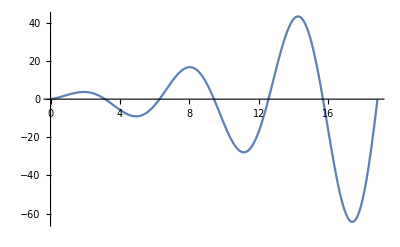

```mathematica
Plot[Exp[x^{1/2}] * Sin[x], {x, 0Pi, 6Pi}]
```

```mathematica
TrigExpand[Sin[2x]]
```

2 Cos[x] Sin[x]

```mathematica
Plot[{∑_(n=0)^40 Log[2]^n/(n!)x^n, 2^x}, {x, 0, 100}]
```

-Graphics-

```mathematica
Manipulate[Plot[{1/x^p}, {x, -10, 10}], {p,-3,3, Appearance-> "Labeled"}]
```

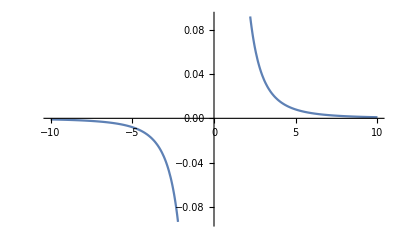

```mathematica
Plot[{1/x^3}, {x, -10, 10}]
```

```mathematica
Manipulate[
Plot[{
Sin[x],
Sin[a]∑_(n=0)^N (-1)^n( (x-a)^(2n)/((2n)!) + (x-a)^(2n+1)/((2n+1)!))
},
{x, -4Pi, 4Pi}],
{{a, 0}, -4Pi, 4Pi ,Appearance->"Labeled"},
{{N, 2}, 1, 10,Appearance->"Labeled"}
]
```

N$$::shdw: Symbol N$$ appears in multiple contexts {System`,Global`}; definitions in context System` may shadow or be shadowed by other definitions.

General::stop: Further output of NSum::nslim will be suppressed during this calculation.

```mathematica
Manipulate[
Plot[{
Sin[x],
∑_(n=0)^N (-1)^n((Sin[a](x-a)^(2n))/((2n)!) + (Cos[a](x-a)^(2n+1))/((2n+1)!))
},
{x, -10Pi, 10Pi}, PlotRange->{-2,2}],
{{a, 0}, -10Pi, 10Pi, Appearance->"Labeled"},
{{N, 2}, 1, 100, Appearance-> "Labeled"}
]
```

```mathematica
Manipulate[Plot[Sin[a x+b],{x,0,6}],
{{a,2},1,4,0.05,Appearance->"Labeled"},
{{b,0},0,10,0.05,Appearance->"Labeled"}]
```

```mathematica
Manipulate[
Plot[Sqrt[x^2 - k], {x, 0, 10}],
{k, 0, 50, 0.05, Appearance -> "Labeled"}
]
```

```mathematica
Manipulate[
Plot3D[a*x*y, {x,-20,20}, {y, -20, 20}, PlotRange->{-2000,2000}],
{{a, 1}, -100, 100, 0.1}
]
```

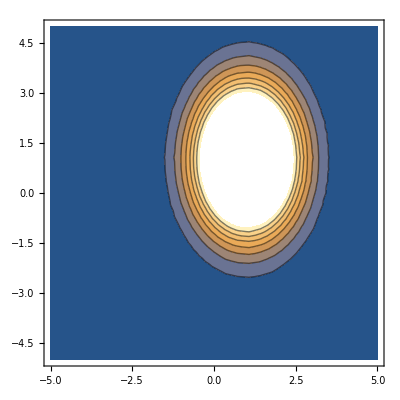

```mathematica
ContourPlot[
PDF[
MultinormalDistribution[{1,1},{{1,0},{0,2}}],
{x,y}
],
{x, -5,5},
{y,-5,5}
]
```

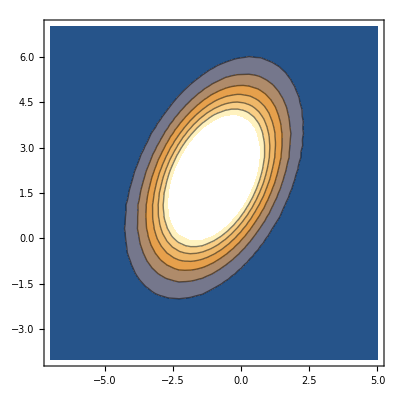

```mathematica
ContourPlot[
PDF[
MultinormalDistribution[{-1,2},{{2,1},{1,3}}],
{x,y}
],
{x, -7,5},
{y,-4,7}
]
```

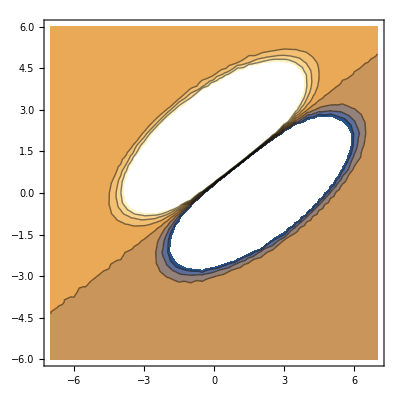

```mathematica
ContourPlot[
PDF[
MultinormalDistribution[{0,2},{{2,1},{1,1}}],
{x,y}
] 
-
PDF[
MultinormalDistribution[{2,0},{{2,1},{1,1}}],
{x,y}
] ,
{x, -7,7},
{y,-6,6}
]
```

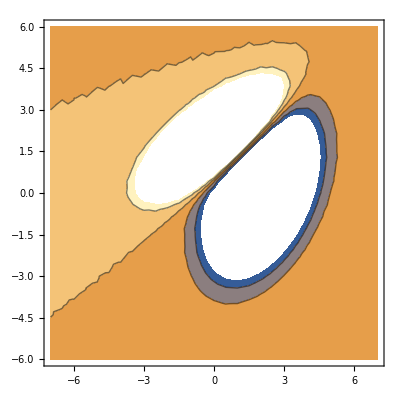

```mathematica
ContourPlot[
PDF[
MultinormalDistribution[{0,2},{{2,1},{1,1}}],
{x,y}
] 
-
PDF[
MultinormalDistribution[{2,0},{{2,1},{1,3}}],
{x,y}
] ,
{x, -7,7},
{y,-6,6}
]
```

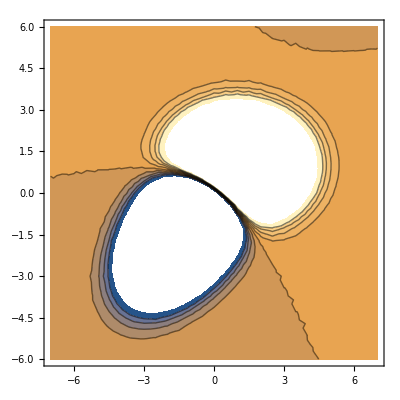

```mathematica
ContourPlot[
PDF[
MultinormalDistribution[{1,1},{{2,0},{0,1}}],
{x,y}
] 
-
PDF[
MultinormalDistribution[{-1,-1},{{2,1},{1,2}}],
{x,y}
] ,
{x, -7,7},
{y,-6,6}
]
```

```mathematica
Plot3D[({{1}, {100}}).({{x1}, {x2}}), 
{x1,-5,5},
{x2,-5,5}
]
```

-Graphics3D-

```mathematica
f[w_] :=Total[w^2]^2
```

```mathematica
D[f[{w1,w2,w3,w4}], w2]
```

4 w2 (w1^2+w2^2+w3^2+w4^2)

```mathematica
Plot[Sin[x]y^2 == x, {x,-9,9},{y,-4,4}]
```

Plot::nonopt: Options expected (instead of {y,-4,4}) beyond position 2 in Plot[Sin[x] y^2==x,{x,-9,9},{y,-4,4}]. An option must be a rule or a list of rules.

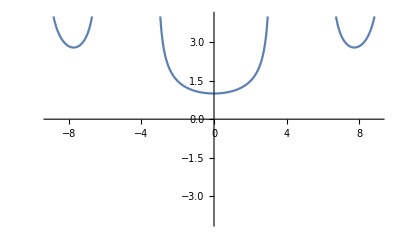

```mathematica
Plot[Sqrt[x/(Sin[x])], {x, -9,9}, PlotRange->{-4,4}]
```

```mathematica
f0=(1-p)^2
```

(1-p)^2

```mathematica
f1 = 2p(1-p)(1-d)
```

2 (1-d) (1-p) p

```mathematica
f2 = p^2(1-d)^2
```

(1-d)^2 p^2

```mathematica
m0=(1-p)
```

1-p

```mathematica
m1 = p(1-d)
```

(1-d) p

```mathematica
RRf =(f1 + f2) / (f1 + f2 + f0)
```

(2 (1-d) (1-p) p+(1-d)^2 p^2)/((1-p)^2+2 (1-d) (1-p) p+(1-d)^2 p^2)

```mathematica
RRm = m1 / (m1 + m0)
```

((1-d) p)/(1-p+(1-d) p)

```mathematica
Simplify[RRf/RRm]
```

(-2+p+d p)/(-1+d p)

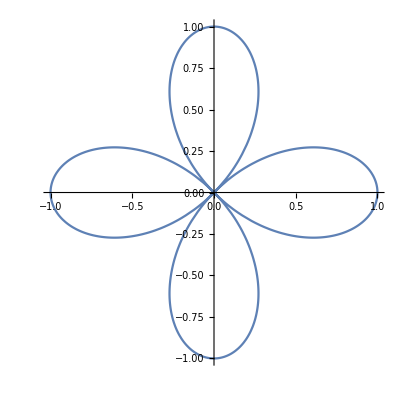

```mathematica
PolarPlot[Cos[2t],{t, 0, 2*Pi}]
```

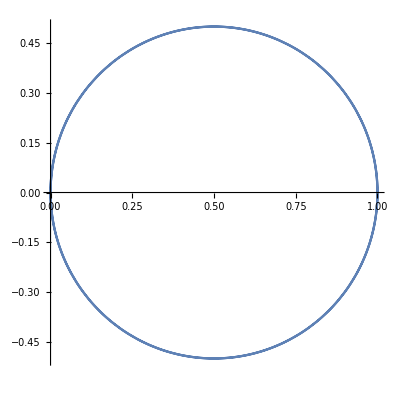

```mathematica
PolarPlot[Cos[t], {t, 0, 2*Pi}]
```

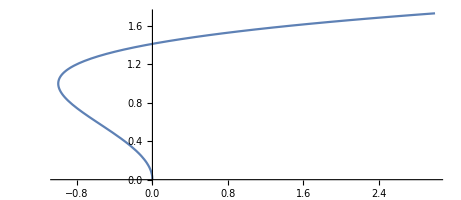

```mathematica
ParametricPlot[{t^2 - 2t, Sqrt[t]}, {t, 0, 3}]
```

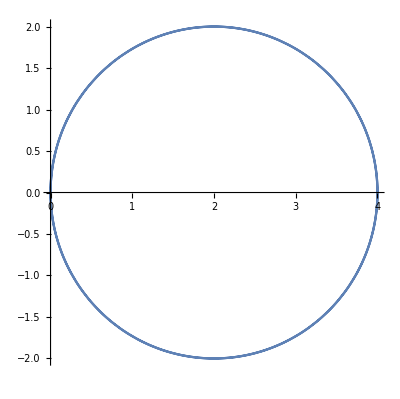

```mathematica
PolarPlot[2*2Cos[t],{t,0,2*Pi}]
```

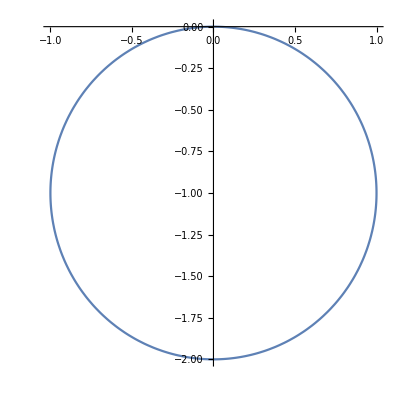

```mathematica
PolarPlot[-2Sin[t], {t, Pi, 2*Pi}]
```

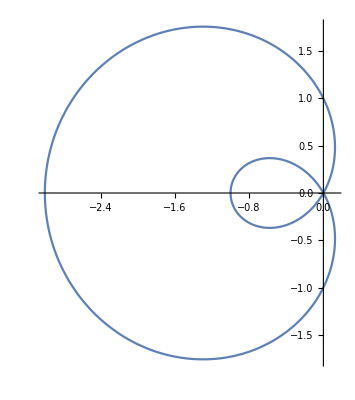

```mathematica
PolarPlot[1 -2Cos[t],{t, 0, 2*Pi}]
```

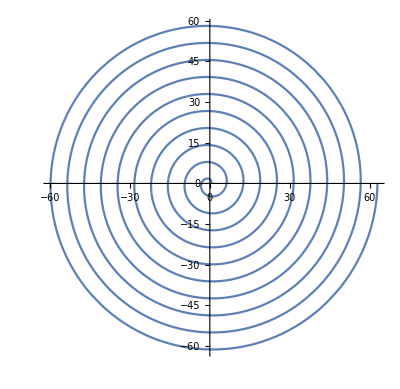

```mathematica
PolarPlot[t, {t, 0, 20*Pi}]
```

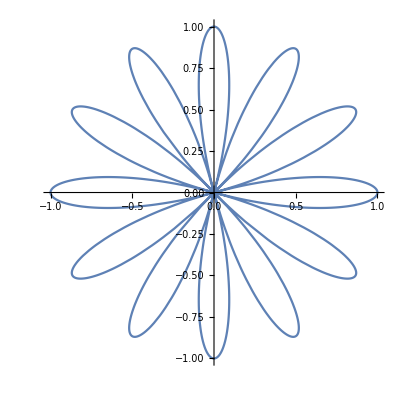

```mathematica
PolarPlot[Cos[6*t],{t,0,2*Pi}]
```

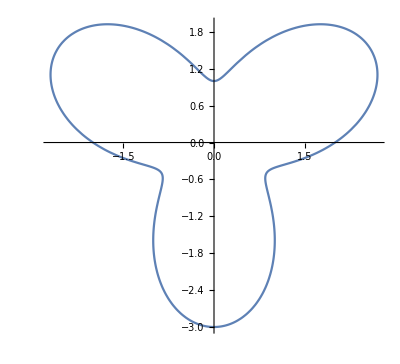

```mathematica
PolarPlot[2 + Sin[3t],{t,0,2*Pi}]
```

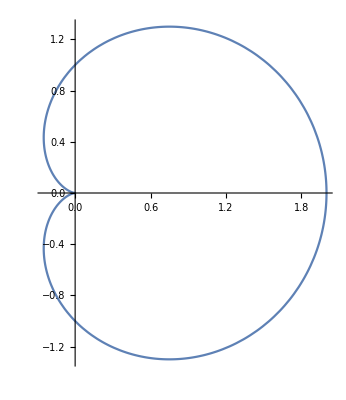

```mathematica
PolarPlot[1 + Cos[t],{t,0,2*Pi}]
```

```mathematica
Integrate[x y(x^2-y^2),{x, 0, b},{y, 0, a}]
```

1/8 (-a^4 b^2+a^2 b^4)

```mathematica
Integrate[x y Cos[y+x^2 y],{y,0,a},{x,0,b}]
```

1/2 (Cos[a]-(b^2+Cos[a (1+b^2)])/(1+b^2))

```mathematica
Limit[Sum[1/(n Log[n]),{n,2,N}],N -> Infinity]
```

```mathematica
Limit[∑_(n=2)^N 1/(n Log[n]),N->∞]
```

```mathematica
Sum[1/n^2,{n,2,Infinity}]
```

-1+π^2/6

```mathematica
Limit[∑_(n=2)^N 1/n^2,N -> Infinity]
```

1/6 (-6+π^2)

```mathematica
{1,2} == {1,2, 2}
```

False

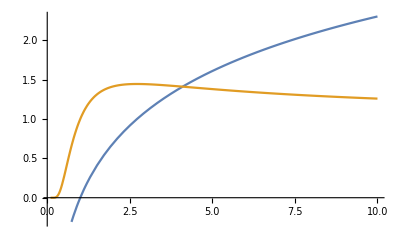

```mathematica
Plot[{Log[x], x^(1/x)},{x,0.1, 10}]
```

```mathematica
B[m_]:=2^(-2^m)2^m
```

```mathematica
Simplify[B[m+1]/B[m]]
```

2^(1-2^(1+m)+2 m)

```mathematica
Limit[B[m+1]/B[m],m->Infinity]
```

0